# Homework 5

## Problem 5.1

An alpha particle is incident on a gold nucleus.The alpha particle raises the gold nucleus to an excited state with excitation energy Eex. Call the direction of the alpha' s initial momentum the z direction. Furthermore, we' ll assume that the scattering is in the x - z plane. (This can be done without any loss of generality.Why?) The particles may be safely treated without relativistic corrections.
Let m be the mass of the alpha particle
       M be the mass of the gold nucleus
       K0 and p0 be the kinetic energy and momentum of the alpha before the collision
       Ka and pa be the kinetic energy and momentum of the alpha after the collision
       theta be the scattering angle of the alpha  (Scattering angles are measured with respect to direction of the incident alpha, the + z direction in this case.)
       K and p be the kinetic energy and momentum of the gold after the collision
       phi be the scattering angle of the gold nucleus.
Refer to the figure below for clarification of these various quantities (Au is the symbol for gold on the periodic table).
-Graphics-

Objective: Find Ka as a function of theta and the initial parameters, m, M, K0, and Eex.

```mathematica
Clear["`*"]
```

## Part A

Write down the the conservation equations you need to solve for this system.

```mathematica
Keq=K0==Ka+K+Eex
pxeq=0==pa*Sin[theta]+p*Sin[phi]
pzeq=p0==pa*Cos[theta]+p*Cos[phi]
```

K0==Eex+K+Ka

0==p Sin[phi]+pa Sin[theta]

p0==p Cos[phi]+pa Cos[theta]

### Solution

```mathematica
Keq$=K0==Ka+K+Eex;
pxeq$=0==pa*Sin[theta]+p*Sin[phi];
pzeq$=p0==pa*Cos[theta]+p*Cos[phi];
Solve[Keq,Ka];
a1$=Ka/.%;
Solve[Keq$,Ka];
a2$=Ka/.%;
Solve[pxeq,pa];
b1$=pa/.%;
Solve[pxeq$,pa];
b2$=pa/.%;
Solve[pzeq,pa];
c1$=pa/.%;
Solve[pzeq$,pa];
c2$=pa/.%;
If[FullSimplify[Solve[a1$==a2$,K]]=={{}},Print["Keq is correct."],Print["Keq is incorrect."]]
If[FullSimplify[Solve[pxeq==pxeq$,pa]]=={{}},Print["pxeq is correct."],Print["pxeq is incorrect."]]
If[FullSimplify[Solve[pzeq==pzeq$,pa]]=={{}},Print["pzeq is correct."],Print["pzeq is incorrect."]]
Keq2$=K0==Ka+K-Eex;
Solve[Keq2$,Ka];
a3$=Ka/.%;
If[FullSimplify[Solve[a1$==a3$,K]]=={{}},Print["K_before = K_after + Eex. Check your signs."]]
```

Keq is correct.

pxeq is correct.

pzeq is correct.

## Part B

Write the momenta in terms of the kinetic energies.

```mathematica
p0=Sqrt[K0*2*m]
p=Sqrt[2*M*K]
pa=Sqrt[Ka*2*m]
```

√2 √(K0 m)

√2 √(K M)

√2 √(Ka m)

### Solutions

```mathematica
p0$=Sqrt[2*m*K0];
p$=Sqrt[2*M*K];
pa$=Sqrt[2*m*Ka];
If[FullSimplify[Solve[p0^2==p0$^2,K0]]=={{}},Print["p0 is correct."],Print["p0 is incorrect."]]
If[FullSimplify[Solve[p^2==p$^2,K]]=={{}},Print["p is correct."],Print["p is incorrect."]]
If[FullSimplify[Solve[pa^2==pa$^2,Ka]]=={{}},Print["pa is correct."],Print["pa is incorrect."]]
```

p0 is correct.

p is correct.

pa is correct.

## Part C

Now let’s view the three equations to verify that we have three equations in three unknowns: K, Ka, and phi (we are treating theta as a known quantity, since it can presumably be measured experimentally).

```mathematica
Print[Keq]
Print[pxeq]
Print[pzeq]
```

K0==Eex+K+Ka

0==√2 √(K M) Sin[phi]+√2 √(Ka m) Sin[theta]

√2 √(K0 m)==√2 √(K M) Cos[phi]+√2 √(Ka m) Cos[theta]

Let's just solve these equations:

```mathematica
Solve[{Keq,pxeq,pzeq},{Ka,K,phi}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ka→(-K0^2 m M-2 Eex K0 m M Cos[theta]^2+159+(2 6 √1)/1-(√2 K0^2 m M 1^4 √(K0 (-Eex+K0)^2 M^2 1^2 (6+K0 m^2 Cos[2 theta]) Sin[theta]^4))/(K0^2 M^2+17+K0^2 M^2 Sin[theta]^4))/(Eex M^2 Sin[theta]^2-K0 M^2 Sin[theta]^2+2 Eex m M Cos[theta]^2 Sin[theta]^2-2 K0 m M Cos[theta]^2 Sin[theta]^2+9+Eex m^2 Sin[theta]^6-K0 m^2 Sin[theta]^6),K→-Eex+K0-1/1,phi→-ArcCos[-√((K0^2 M^2)/(K0^2 M^2+17+1)+23)]},{1},4,{1},1}
 |  |  |  |

It’s clear that this solution is impractical, so we’ll try a simpler approach. We can solve for Sin[phi] and Cos[phi] using the momentum conservation equations and then use the identity Sin[phi]^2+Cos[phi]^2=1 to eliminate phi. This is what we would do if we were solving the equations by hand.

Use the appropriate momentum conservation equations to solve for Cos[phi] and Sin[phi]:

```mathematica
cosphi=Solve[pzeq,Cos[phi]]
sinphi=Solve[pxeq,Sin[phi]]
```

{{Cos[phi]→(√(K0 m)-√(Ka m) Cos[theta])/(√(K M))}}

{{Sin[phi]→-(√(Ka m) Sin[theta])/(√(K M))}}

### Solutions

```mathematica
cosphi$=Solve[pzeq,Cos[phi]];
sinphi$=Solve[pxeq,Sin[phi]];
If[FullSimplify[Solve[cosphi==cosphi$,Ka]]=={{}},Print["cosphi is correct."],Print["cosphi is incorrect."]]
If[FullSimplify[Solve[sinphi==sinphi$,Ka]]=={{}},Print["sinphi is correct."],Print["sinphi is incorrect."]]
```

cosphi is correct.

sinphi is correct.

## Part D

In the cell below, we use the fact that sin^2(phi) + cos^2(phi) = 1 to solve for Ka in terms of theta, m, M, K0, and Eex. The “/.” is shorthand for ReplaceAll. It’s a means of making substitutions. We will perform a few simplifications and substitutions along the way.
Note that exp1 is a list enclosed into sets of brackets. exp1[ [1] ] [ [1] ] takes the equation out of the brackets.
Also note that solutions are returned in substitution, not as a simple expression.

```mathematica
exp1=1==Cos[phi]^2+Sin[phi]^2/.cosphi/.sinphi
exp2=FullSimplify[exp1[[1]][[1]]];
(* Use your original kinetic energy equation to make the appropriate substitution to obtain exp3. *)
exp3=exp2/.K->K0-Ka-Eex; 
sols=Solve[exp3,Ka];
Ka1=FullSimplify[Ka/.sols[[1]][[1]]]
Ka2=FullSimplify[Ka/.sols[[2]][[1]]]
```

{{1==(√(K0 m)-√(Ka m) Cos[theta])^2/(K M)+(Ka m Sin[theta]^2)/(K M)}}

(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]-√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))/(m+M)^2

(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))/(m+M)^2

It turns out that these solutions are not both physically meaningful for over the full range of theta. We shall see this in the next problem.

### Hint

You need to subsitute K0-Ka-Eex for K.

### Solutions

```mathematica
Ka1$=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]-√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))
Ka2$=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))
If[FullSimplify[Solve[Ka1$==Ka1,K0]]=={{}} ||FullSimplify[Solve[Ka2$==Ka1,K0]]=={{}} ,Print["Ka1 is correct."],Print["Ka1 is incorrect."]]
If[FullSimplify[Solve[Ka1$==Ka2,K0]]=={{}} ||FullSimplify[Solve[Ka2$==Ka2,K0]]=={{}} ,Print["Ka2 is correct."],Print["Ka2 is incorrect."]]
```

(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]-√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))/(m+M)^2

(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))/(m+M)^2

Ka1 is correct.

Ka2 is correct.

## Problem 5.2

Now we will calculate some numerical values for the scattering described in Problem 5.1.  The alpha has a kinetic energy of 6.0 MeV (1.0 MeV=1.602e-13 J). The masses of the particles are given in kg below.

Make a plot of Ka as a function of theta for Eex=0 and 0.7654 MeV.

```mathematica
Clear["`*"]
```

```mathematica
m=6.6436*10^(-27);
M=3.2695*10^(-25);
K0=6*1.602*10^(-13);
```

Copy each solution from Problem 5.1 Part D and insert it into the appropriate line below to define Ka as a function of theta and Eex.

8.98596×10^48 (1.02749×10^-61-1.09068×10^-49 Eex-9.21139×10^-33 √(Cos[theta]^2 (2.05455×10^-61-2.18137×10^-49 Eex+4.24249×10^-65 Cos[2 theta]))+4.24249×10^-65 Cos[2 theta])

8.98596×10^48 (1.02749×10^-61-1.09068×10^-49 Eex+9.21139×10^-33 √(Cos[theta]^2 (2.05455×10^-61-2.18137×10^-49 Eex+4.24249×10^-65 Cos[2 theta]))+4.24249×10^-65 Cos[2 theta])

8.98596×10^48 (1.02749×10^-61-1.09068×10^-49 Eex+9.21139×10^-33 Cos[theta] √(2.05455×10^-61-2.18137×10^-49 Eex+4.24249×10^-65 Cos[2 theta])+4.24249×10^-65 Cos[2 theta])

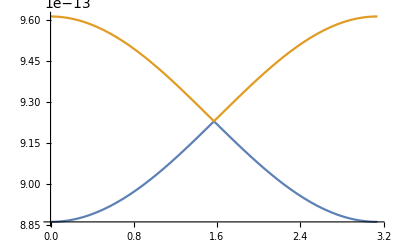

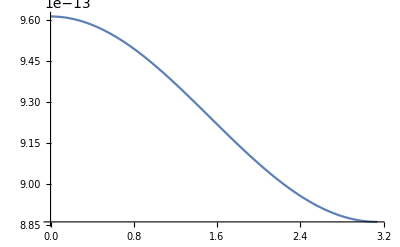

```mathematica
Ka1[theta_,Eex_]=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]-√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))
Ka2[theta_,Eex_]=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 √(K0 m^2 Cos[theta]^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))
Ka3[theta_,Eex_]=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 Cos[theta] √(K0 m^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])))
Plot[{Ka1[theta,0],Ka2[theta,0]},{theta,0,Pi}]
Plot[Ka3[theta,0],{theta,0,Pi}]
```

Notice how the two solutions seem to "trade places" when theta reaches Pi/2.

But what is the correct solution?

To determine this, we will plot sin^2(phi)+cos^2(phi) using each solution Ka1 and Ka2 above and see which one gives us the required value of 1 for various ranges of theta. In the cell below, we will first rewrite the equations from Problem 5.1, but this time explicitly including the functional notation f[theta,Eex], so that we can plot everything as a function of theta for a given value of Eex. In the first line, set Ka[theta_,Eex_] initially to Ka1[theta,Eex], and then try it again with Ka2.

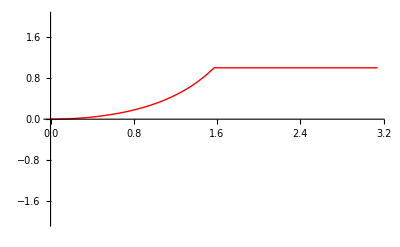

```mathematica
Ka[theta_,Eex_]=Ka1[theta,Eex];
p0=Sqrt[K0*2*m];(* express it in terms of the initial energy of the alpha particle *)
pa[theta_,Eex_]=Sqrt[2*m*Ka[theta,Eex]];
K[theta_,Eex_]=K0-Ka[theta,Eex]-Eex;
p[theta_,Eex_]=Sqrt[2*M*K[theta,Eex]];
sinphi[theta_,Eex_]=-pa[theta,Eex]*Sin[theta]/p[theta,Eex];
cosphi[theta_,Eex_]=(p0-pa[theta,Eex]*Cos[theta])/p[theta,Eex];
Plot[(cosphi[theta,0])^2+(sinphi[theta,0])^2,{theta,0,Pi},PlotStyle->{Red,Thick},PlotRange->2]
```

### Solutions

```mathematica
p0$=Sqrt[2*m*K0];
pa$[theta_,Eex_]=Sqrt[2*m*Ka[theta,Eex]];
K$[theta_,Eex_]=K0-Ka[theta,Eex]-Eex;
p$[theta_,Eex_]=Sqrt[2*M*K[theta,Eex]];
sinphi$[theta_,Eex_]=-pa[theta,Eex]*Sin[theta]/p[theta,Eex];
cosphi$[theta_,Eex_]=(p0-pa[theta,Eex]*Cos[theta])/p[theta,Eex];
If[FullSimplify[Solve[p0==p0$]]=={{}},Print["p0 is correct."],Print["p0 is incorrect."]]
If[FullSimplify[Solve[pa[a,b]==pa$[a,b]]]=={{}},Print["pa is correct."],Print["pa is incorrect."]]
If[FullSimplify[Solve[K[a,b]==K$[a,b]]]=={{}},Print["K is correct."],Print["K is incorrect."]]
If[FullSimplify[Solve[p[a,b]==p$[a,b]]]=={{}},Print["p is correct."],Print["p is incorrect."]]
If[FullSimplify[Solve[sinphi[a,b]==sinphi$[a,b]]]=={{}},Print["sinphi is correct."],Print["sinphi is incorrect."]]
If[FullSimplify[Solve[cosphi[a,b]==cosphi$[a,b]]]=={{}},Print["cosphi is correct."],Print["cosphi is incorrect."]]
```

p0 is correct.

pa is correct.

K is correct.

p is correct.

sinphi is correct.

cosphi is correct.

### Simplifying the Solutions

So you see that one solution is good over half the range and the other is good over the other half of the range. At this point we can invoke a little trick to make life easier. Note that the two roots - roots of a quadratic equation - differ only by the sign of the square root, which is:
√(K0 m^2 Cos[theta]^2 (-(m+M) (K0 (m-M)+Eex M)+K0 m^2 Cos[theta]^2))
If we factor out Cos[theta] from the radical, the cosine automatically changes sign when theta reaches Pi/2:
Cos[theta] √(K0 m^2 (-(m+M) (K0 (m-M)+Eex M)+K0 m^2 Cos[theta]^2))
With this trick, we can define a single expression that gives the correct solution for the full range of theta. We will call it Ka3, defined below. Copy and paste the previous cell and set Ka to Ka3 to verify that sin^2(phi) + cos^2(phi) = 1 over the whole range.

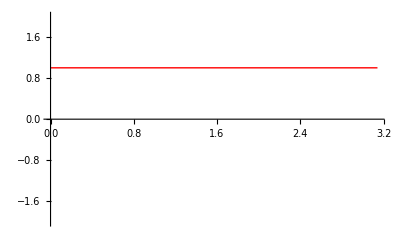

```mathematica
Ka3[theta_,Eex_]=1/(m+M)^2(K0 M^2-Eex M (m+M)+K0 m^2 Cos[2 theta]+√2 Cos[theta] √(K0 m^2 (-2 Eex M (m+M)-K0 (m^2-2 M^2)+K0 m^2 Cos[2 theta])));
Ka[theta_,Eex_]=Ka3[theta,Eex];
p0=Sqrt[K0*2*m];(* express it in terms of the initial energy of the alpha particle *)
pa[theta_,Eex_]=Sqrt[2*m*Ka[theta,Eex]];
K[theta_,Eex_]=K0-Ka[theta,Eex]-Eex;
p[theta_,Eex_]=Sqrt[2*M*K[theta,Eex]];
sinphi[theta_,Eex_]=-pa[theta,Eex]*Sin[theta]/p[theta,Eex];
cosphi[theta_,Eex_]=(p0-pa[theta,Eex]*Cos[theta])/p[theta,Eex];
Plot[(cosphi[theta,0])^2+(sinphi[theta,0])^2,{theta,0,Pi},PlotStyle->{Red,Thick},PlotRange->2]
```

### Final Plots

Now we wish to plot Ka in MeV vs theta in degrees. Why does it make sense that the alpha particle has a lower energy for large scattering angles?

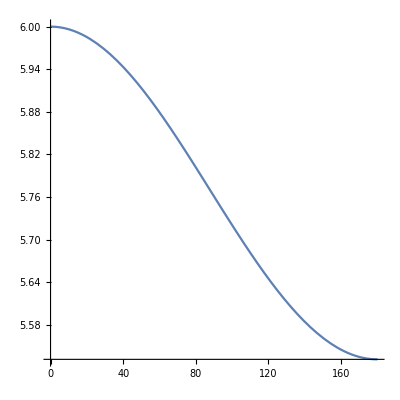

```mathematica
ParametricPlot[{theta*180/Pi,Ka[theta,0]/(1.602*10^(-13))},{theta,0,Pi},AspectRatio->1/1]
```

Then try the same plot with the excitation energy Eex = 0.7654 MeV. Note that we need Eex in joules, so I've included a conversion factor.
Finally, we'll plot the difference between the alpha energies for the two excitation energies of the Au nucleus. This difference is near the excitation energy at all angles, but particularly so at small angles.

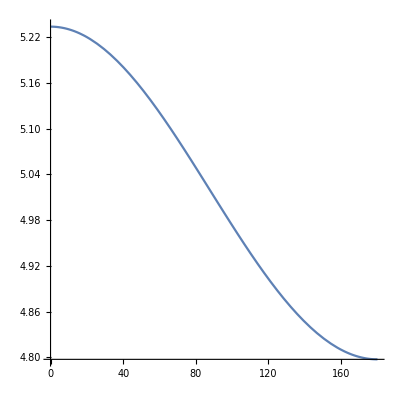

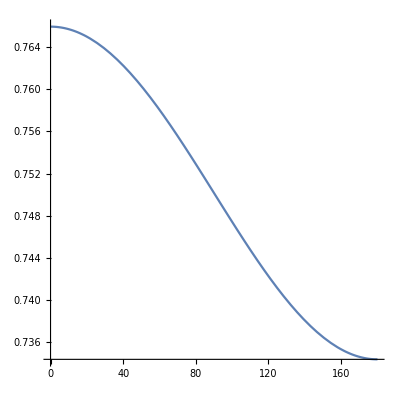

```mathematica
ParametricPlot[{theta*180/Pi,Ka[theta,0.7654*1.602*10^(-13)]/(1.602*10^(-13))},{theta,0,Pi},AspectRatio->1/1]
ParametricPlot[{theta*180/Pi,(Ka[theta,0]-Ka[theta,0.7654*1.602*10^(-13)])/(1.602*10^(-13))},{theta,0,Pi},AspectRatio->1/1]
```

## Paper Problems

-Graphics-